```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\Time.xlsx"]
```

```mathematica
data={{3.,0.029},{5.,0.052},{7.,0.075},{10.,0.111},{12.,0.128},{15.,0.161},{20.,0.215},{25.,0.263},{30.,0.33},{40.,0.397},{50.,0.497}}
```

{{3.,0.029},{5.,0.052},{7.,0.075},{10.,0.111},{12.,0.128},{15.,0.161},{20.,0.215},{25.,0.263},{30.,0.33},{40.,0.397},{50.,0.497}}

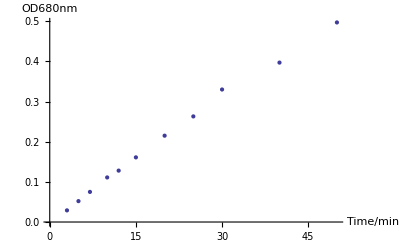

```mathematica
gra=ListPlot[data,AxesLabel->{"Time/min","OD680nm"}]
```

```mathematica
gra2=LinearModelFit[data,x,x]
```

```mathematica
Normal[gra2]
```

0.00858421+0.00997039 x

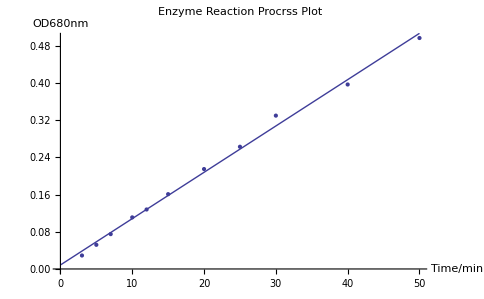

```mathematica
Show[gra,Plot[gra2[x],{x,0,50}],PlotLabel-> "Enzyme Reaction Procrss Plot"]
```

```mathematica
gra2["RSquared"]
```

0.99589